```mathematica
ClearAll["Global`*"]
```

Potential Series Terms

```mathematica
3(1+q)== a[0] + a[2]+b[0] + b[2]+e[0] +e[2]+f[0]+f[2]+g[0]+g[2] ;
945/16 (1+q)+3 (2q+(1+q)μ)==6/5 μ(a[0]+a[2])+a[0]+2a[2]+4/5 μ(b[0]+b[2])+b[0]+2b[2]+2/5 μ(e[0]+e[2])+(e[0]+2e[2])+f[0]+2f[2]-2/5 μ(g[0]+g[2])+g[0]+2g[2];
```

Asymptotic Series Terms

```mathematica
a[2]== 4.755874437709627 q μ^(-1/5);
b[2]== 1.1258579126708648 q μ^(1/5);
e[2]==-0.6640638150134823 q μ^(3/5);
f[2]==0.1448677094951177 q μ;
g[2]==-0.010362039589544165 q μ^(7/5);
(4.755874437709627+0.004115002962959785 q)== μ^(1/5) (a[0]+(2 a[2])/(5 μ));
```

Intermediate Points Terms

```mathematica
(1+2.25 q) 4.839155973899763== (1+0.5 μ)^(1/5) (a[0]+2.25 a[2])+1/(1+0.5 μ)^(1/5) (b[0]+2.25 b[2])+1/(1+0.5 μ)^(3/5) (e[0]+2.25 e[2])+1/(1+0.5 μ) (f[0]+2.25 f[2])+1/(1+0.5 μ)^(7/5) (g[0]+2.25 g[2]);
```

```mathematica
(1+4 q) 5.368777985060538== (1+μ)^(1/5) (a[0]+4 a[2])+1/(1+μ)^(1/5) (b[0]+4 b[2])+1/(1+μ)^(3/5) (e[0]+4 e[2])+1/(1+μ) (f[0]+4 f[2])+1/(1+μ)^(7/5) (g[0]+4 g[2]);
```

```mathematica
(1+9 q) 5.999607406557876== (1+2 μ)^(1/5) (a[0]+9 a[2])+1/(1+2 μ)^(1/5) (b[0]+9 b[2])+1/(1+2 μ)^(3/5) (e[0]+9 e[2])+1/(1+2 μ) (f[0]+9 f[2])+1/(1+2 μ)^(7/5) (g[0]+9 g[2])
```

5.99961 (1+9 q)==(1+2 μ)^(1/5) (a[0]+9 a[2])+(b[0]+9 b[2])/(1+2 μ)^(1/5)+(e[0]+9 e[2])/(1+2 μ)^(3/5)+(f[0]+9 f[2])/(1+2 μ)+(g[0]+9 g[2])/(1+2 μ)^(7/5)

```mathematica
(1+36 q) 7.01093057783317== (1+5 μ)^(1/5) (a[0]+36 a[2])+1/(1+5 μ)^(1/5) (b[0]+36 b[2])+1/(1+5 μ)^(3/5) (e[0]+36 e[2])+1/(1+5 μ) (f[0]+36 f[2])+1/(1+5 μ)^(7/5) (g[0]+36 g[2]);
```

```mathematica
(1+169 q) 8.195812837023599== (1+12 μ)^(1/5) (a[0]+169 a[2])+1/(1+12 μ)^(1/5) (b[0]+169 b[2])+1/(1+12 μ)^(3/5) (e[0]+169 e[2])+1/(1+12 μ) (f[0]+169 f[2])+1/(1+12 μ)^(7/5) (g[0]+169 g[2]);
```

```mathematica
(1+324 q) 8.734742688960848== (1+17 μ)^(1/5) (a[0]+324 a[2])+1/(1+17 μ)^(1/5) (b[0]+324 b[2])+1/(1+17 μ)^(3/5) (e[0]+324 e[2])+1/(1+17 μ) (f[0]+324 f[2])+1/(1+17 μ)^(7/5) (g[0]+324 g[2]);
```

```mathematica
(1+2025 q) 10.474414623958456== (1+45 μ)^(1/5) (a[0]+2025 a[2])+1/(1+45 μ)^(1/5) (b[0]+2025 b[2])+1/(1+45 μ)^(3/5) (e[0]+2025 e[2])+1/(1+45 μ) (f[0]+2025 f[2])+1/(1+45 μ)^(7/5) (g[0]+2025 g[2]);
```

```mathematica
μ=9;
```

Matriz Solución

```mathematica
{c,m}=CoefficientArrays[{3(1+q)== a[0] + a[2]+b[0] + b[2]+e[0] +e[2]+f[0]+f[2]+g[0]+g[2],
945/16 (1+q)+3 (2q+(1+q)μ)==6/5 μ(a[0]+a[2])+a[0]+2a[2]+4/5 μ(b[0]+b[2])+b[0]+2b[2]+2/5 μ(e[0]+e[2])+(e[0]+2e[2])+f[0]+2f[2]-2/5 μ(g[0]+g[2])+g[0]+2g[2],
a[2]== 4.755874437709627 q μ^(-1/5),
b[2]== 1.1258579126708648 q μ^(1/5),
e[2]==-0.6640638150134823 q μ^(3/5),
f[2]==0.1448677094951177 q μ,
g[2]==-0.010362039589544165 q μ^(7/5),
(1+4 q) 5.368777985060538== (1+μ)^(1/5) (a[0]+4 a[2])+1/(1+μ)^(1/5) (b[0]+4 b[2])+1/(1+μ)^(3/5) (e[0]+4 e[2])+1/(1+μ) (f[0]+4 f[2])+1/(1+μ)^(7/5) (g[0]+4 g[2]),(1+36 q) 7.01093057783317== (1+5 μ)^(1/5) (a[0]+36 a[2])+1/(1+5 μ)^(1/5) (b[0]+36 b[2])+1/(1+5 μ)^(3/5) (e[0]+36 e[2])+1/(1+5 μ) (f[0]+36 f[2])+1/(1+5 μ)^(7/5) (g[0]+36 g[2]),
(1+324 q) 8.734742688960848== (1+17 μ)^(1/5) (a[0]+324 a[2])+1/(1+17 μ)^(1/5) (b[0]+324 b[2])+1/(1+17 μ)^(3/5) (e[0]+324 e[2])+1/(1+17 μ) (f[0]+324 f[2])+1/(1+17 μ)^(7/5) (g[0]+324 g[2]),
(1+2025 q) 10.474414623958456== (1+45 μ)^(1/5) (a[0]+2025 a[2])+1/(1+45 μ)^(1/5) (b[0]+2025 b[2])+1/(1+45 μ)^(3/5) (e[0]+2025 e[2])+1/(1+45 μ) (f[0]+2025 f[2])+1/(1+45 μ)^(7/5) (g[0]+2025 g[2])},{a[0],a[2],b[0],b[2],e[0],e[2],f[0],f[2],g[0],g[2],q}]
```

{SparseArray[…],SparseArray[…]}

Solución a Sistema de Ecuaciones

```mathematica
sol = LinearSolve[m,-c]
```

{2.68481,0.0018935,6.51268,0.00107948,-27.4342,-0.00153334,50.672,0.000805561,-29.4356,-0.000138762,0.000617852}

Coeficientes

```mathematica
a[0]=a[0]/.a[0]->sol[[1]];
a[2]=a[2]/.a[2]->sol[[2]];
b[0]=b[0]/.b[0]->sol[[3]];
b[2]=b[2]/.b[2]->sol[[4]];
e[0]=e[0]/.e[0]-> sol[[5]];
e[2]=e[2]/.e[2]-> sol[[6]];
f[0]=f[0]/.f[0]->sol[[7]];
f[2]=f[2]/.f[2]->sol[[8]];
g[0]=g[0]/.g[0]->sol[[9]];
g[2]=g[2]/.g[2]->sol[[10]];
q=q/.q->sol[[11]];
```

Ecuaciones Utilizadas

```mathematica
3(1+q)== a[0] + a[2]+b[0] + b[2]+e[0] +e[2]+f[0]+f[2]+g[0]+g[2]
945/16 (1+q)+3 (2q+(1+q)μ)==6/5 μ(a[0]+a[2])+a[0]+2a[2]+4/5 μ(b[0]+b[2])+b[0]+2b[2]+2/5 μ(e[0]+e[2])+(e[0]+2e[2])+f[0]+2f[2]-2/5 μ(g[0]+g[2])+g[0]+2g[2]
a[2]== 4.755874437709627 q μ^(-1/5)
b[2]== 1.1258579126708648 q μ^(1/5)
e[2]==-0.6640638150134823 q μ^(3/5)
f[2]==0.1448677094951177 q μ
g[2]==-0.010362039589544165 q μ^(7/5)
(1+4 q) 5.368777985060538== (1+μ)^(1/5) (a[0]+4 a[2])+1/(1+μ)^(1/5) (b[0]+4 b[2])+1/(1+μ)^(3/5) (e[0]+4 e[2])+1/(1+μ) (f[0]+4 f[2])+1/(1+μ)^(7/5) (g[0]+4 g[2])
(1+36 q) 7.01093057783317== (1+5 μ)^(1/5) (a[0]+36 a[2])+1/(1+5 μ)^(1/5) (b[0]+36 b[2])+1/(1+5 μ)^(3/5) (e[0]+36 e[2])+1/(1+5 μ) (f[0]+36 f[2])+1/(1+5 μ)^(7/5) (g[0]+36 g[2])
(1+324 q) 8.734742688960848== (1+17 μ)^(1/5) (a[0]+324 a[2])+1/(1+17 μ)^(1/5) (b[0]+324 b[2])+1/(1+17 μ)^(3/5) (e[0]+324 e[2])+1/(1+17 μ) (f[0]+324 f[2])+1/(1+17 μ)^(7/5) (g[0]+324 g[2])
(1+2025 q) 10.474414623958456== (1+45 μ)^(1/5) (a[0]+2025 a[2])+1/(1+45 μ)^(1/5) (b[0]+2025 b[2])+1/(1+45 μ)^(3/5) (e[0]+2025 e[2])+1/(1+45 μ) (f[0]+2025 f[2])+1/(1+45 μ)^(7/5) (g[0]+2025 g[2])
```

True

True

True

«1 more identical outputs»

False

True

True

True

«3 more identical outputs»

Aproximante

```mathematica
Eapp[λ_]:=(1+μ λ)^(1/5)  (a[0]+a[2] (1+λ)^2)/(1+q (1+λ)^2)+(1+μ λ)^(- 1/5)(b[0]+b[2] (1+λ)^2)/(1+q (1+λ)^2)+(1+μ λ)^(- 3/5)(e[0]+e[2] (1+λ)^2)/(1+q (1+λ)^2)+(1+μ λ)^(- 1)(f[0]+f[2] (1+λ)^2)/(1+q (1+λ)^2)+(1+μ λ)^(- 7/5)(g[0]+g[2] (1+λ)^2)/(1+q (1+λ)^2);
```

```mathematica
?Eapp
```

```mathematica
Eapp[17]
```

8.73474

```mathematica
data=Table[{λ,Eapp[λ]},{λ,0.0,100,1}];
```

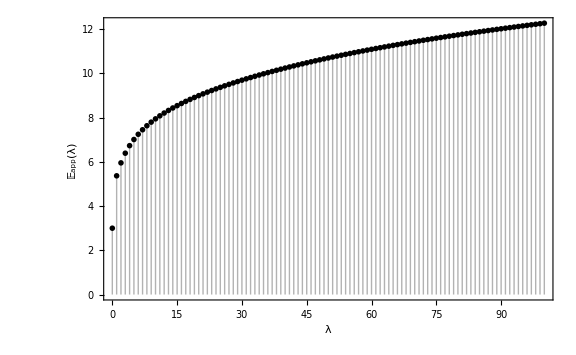

```mathematica
ListPlot[data,Frame->True,FrameLabel->{"λ","𝔼_app(λ)"},PlotRange->All,Filling->Axis,PlotTheme->"Monochrome",ImageSize->Large]
```

## Exact Values

```mathematica
eqnex[enex_]:=-uex''[x]+(x^2+0 x^8-enex) uex[x]
L=5;
wavefuncex[enex_]:=NDSolve[{eqnex[enex]==0,uex[-L]==1,uex'[-L]==0},uex,{x,-L,0},Method->"Shooting", MaxSteps->1000]
```

```mathematica
solex[x_?NumericQ,enex_?NumericQ]:=uex[x]/.wavefuncex[enex][[1]]
```

```mathematica
solprimeex[x_?NumericQ,enex_?NumericQ]:=uex'[x]/.wavefuncex[enex][[1]]
```

```mathematica
evalueex=enex/.FindRoot[solex[0,enex],{enex,2.5,3.5}]
```

3.

```mathematica
NumberForm[evalueex,16]
```

3.000000012633707

```mathematica
eex[0]=evalueex;
```

```mathematica
eqnex1[enex1_]:=-uex1''[x]+(x^2+0.5 x^8-enex1) uex1[x]
L=2.51969;
wavefuncex1[enex1_]:=NDSolve[{eqnex1[enex1]==0,uex1[-L]==1,uex1'[-L]==0},uex1,{x,-L,0}]
```

```mathematica
solex1[x_?NumericQ,enex1_?NumericQ]:=uex1[x]/.wavefuncex1[enex1][[1]]
```

```mathematica
solprimeex1[x_?NumericQ,enex1_?NumericQ]:=uex1'[x]/.wavefuncex1[enex1][[1]]
```

```mathematica
evalueex1=enex1/.FindRoot[solex1[0,enex1],{enex1,2.5,3.5}]
```

4.83916

```mathematica
NumberForm[evalueex1,16]
```

4.839155973899763

```mathematica
eex[1]=evalueex1;
```

```mathematica
eqnex2[enex2_]:=-uex2''[x]+(x^2+1.0 x^8-enex2) uex2[x]
L=2.50540;
wavefuncex2[enex2_]:=NDSolve[{eqnex2[enex2]==0,uex2[-L]==1,uex2'[-L]==0},uex2,{x,-L,0},Method->"Shooting", MaxSteps->1000]
```

```mathematica
solex2[x_?NumericQ,enex2_?NumericQ]:=uex2[x]/.wavefuncex2[enex2][[1]]
```

```mathematica
solprimeex2[x_?NumericQ,enex2_?NumericQ]:=uex2'[x]/.wavefuncex2[enex2][[1]]
```

```mathematica
evalueex2=enex2/.FindRoot[solex2[0,enex2],{enex2,2.5,3.5}]
```

5.36878

```mathematica
NumberForm[evalueex2,16]
```

5.368777985060538

```mathematica
eex[2]=evalueex2;
```

```mathematica
eqnex3[enex3_]:=-uex3''[x]+(x^2+2.0 x^8-enex3) uex3[x]
L=2.42001;
wavefuncex3[enex3_]:=NDSolve[{eqnex3[enex3]==0,uex3[-L]==1,uex3'[-L]==0},uex3,{x,-L,0}]
```

```mathematica
solex3[x_?NumericQ,enex3_?NumericQ]:=uex3[x]/.wavefuncex3[enex3][[1]]
```

```mathematica
solprimeex3[x_?NumericQ,enex3_?NumericQ]:=uex3'[x]/.wavefuncex3[enex3][[1]]
```

```mathematica
evalueex3=enex3/.FindRoot[solex3[0,enex3],{enex3,2.5,3.5}]
```

5.99961

```mathematica
NumberForm[evalueex3,16]
```

5.999607406557876

```mathematica
eex[3]=evalueex3;
```

```mathematica
eqnex4[enex4_]:=-uex4''[x]+(x^2+5.0 x^8-enex4) uex4[x]
L=2.10791;
wavefuncex4[enex4_]:=NDSolve[{eqnex4[enex4]==0,uex4[-L]==1,uex4'[-L]==0},uex4,{x,-L,0}]
```

```mathematica
solex4[x_?NumericQ,enex4_?NumericQ]:=uex4[x]/.wavefuncex4[enex4][[1]]
```

```mathematica
solprimeex4[x_?NumericQ,enex4_?NumericQ]:=uex4'[x]/.wavefuncex4[enex4][[1]]
```

```mathematica
evalueex4=enex4/.FindRoot[solex4[0,enex4],{enex4,2.5,3.5}]
```

7.01093

```mathematica
NumberForm[evalueex4,16]
```

7.01093057783317

```mathematica
eex[4]=evalueex4;
```

```mathematica
eqnex5[enex5_]:=-uex5''[x]+(x^2+12 x^8-enex5) uex5[x]
L=1.9746;
wavefuncex5[enex5_]:=NDSolve[{eqnex5[enex5]==0,uex5[-L]==1,uex5'[-L]==0},uex5,{x,-L,0}]
```

```mathematica
solex5[x_?NumericQ,enex5_?NumericQ]:=uex5[x]/.wavefuncex5[enex5][[1]]
```

```mathematica
solprimeex5[x_?NumericQ,enex5_?NumericQ]:=uex5'[x]/.wavefuncex5[enex5][[1]]
```

```mathematica
evalueex5=enex5/.FindRoot[solex5[0,enex5],{enex5,2.5,3.5}]
```

8.19581

```mathematica
NumberForm[evalueex5,16]
```

8.1958128370236

```mathematica
eex[5]=evalueex5;
```

```mathematica
eqnex6[enex6_]:=-uex6''[x]+(x^2+17 x^8-enex6) uex6[x]
L=1.819;
wavefuncex6[enex6_]:=NDSolve[{eqnex6[enex6]==0,uex6[-L]==1,uex6'[-L]==0},uex6,{x,-L,0}]
```

```mathematica
solex6[x_?NumericQ,enex6_?NumericQ]:=uex6[x]/.wavefuncex6[enex6][[1]]
```

```mathematica
solprimeex6[x_?NumericQ,enex6_?NumericQ]:=uex6'[x]/.wavefuncex6[enex6][[1]]
```

```mathematica
evalueex6=enex6/.FindRoot[solex6[0,enex6],{enex6,2.5,3.5}]
```

8.73474

```mathematica
NumberForm[evalueex6,16]
```

8.73474268896085

```mathematica
eex[6]=evalueex6;
```

```mathematica
eqnex7[enex7_]:=-uex7''[x]+(x^2+20.0 x^8-enex7) uex7[x]
L=1.78699;
wavefuncex7[enex7_]:=NDSolve[{eqnex7[enex7]==0,uex7[-L]==1,uex7'[-L]==0},uex7,{x,-L,0}]
```

```mathematica
solex7[x_?NumericQ,enex7_?NumericQ]:=uex7[x]/.wavefuncex7[enex7][[1]]
```

```mathematica
solprimeex7[x_?NumericQ,enex7_?NumericQ]:=uex7'[x]/.wavefuncex7[enex7][[1]]
```

```mathematica
evalueex7=enex7/.FindRoot[solex7[0,enex7],{enex7,2.5,3.5}]
```

9.00051

```mathematica
NumberForm[evalueex7,16]
```

9.00051163633515

```mathematica
eex[7]=evalueex7;
```

```mathematica
eqnex8[enex8_]:=-uex8''[x]+(x^2+45 x^8-enex8) uex8[x]
L=1.7801;
wavefuncex8[enex8_]:=NDSolve[{eqnex8[enex8]==0,uex8[-L]==1,uex8'[-L]==0},uex8,{x,-L,0}]
```

```mathematica
solex8[x_?NumericQ,enex8_?NumericQ]:=uex8[x]/.wavefuncex8[enex8][[1]]
```

```mathematica
solprimeex8[x_?NumericQ,enex8_?NumericQ]:=uex8'[x]/.wavefuncex8[enex8][[1]]
```

```mathematica
evalueex8=enex8/.FindRoot[solex8[0,enex8],{enex8,2.5,3.5}]
```

10.4744

```mathematica
NumberForm[evalueex8,16]
```

10.47441462395846

```mathematica
eex[8]=evalueex8;
```

```mathematica
eqnex11[enex11_]:=-uex11''[x]+(x^2+88 x^8-enex11) uex11[x]
L=1.6019;
wavefuncex11[enex11_]:=NDSolve[{eqnex11[enex11]==0,uex11[-L]==1,uex11'[-L]==0},uex11,{x,-L,0}]
```

```mathematica
solex11[x_?NumericQ,enex11_?NumericQ]:=uex11[x]/.wavefuncex11[enex11][[1]]
```

```mathematica
solprimeex11[x_?NumericQ,enex11_?NumericQ]:=uex11'[x]/.wavefuncex11[enex11][[1]]
```

```mathematica
evalueex11=enex11/.FindRoot[solex11[0,enex11],{enex11,2.5,3.5}]
```

11.8999

```mathematica
NumberForm[evalueex11,16]
```

11.89986169260856

```mathematica
eex[9]=evalueex11;
```

```mathematica
eqnex10[enex10_]:=-uex10''[x]+(x^2+100 x^8-enex10) uex10[x]
L=1.6019;
wavefuncex10[enex10_]:=NDSolve[{eqnex10[enex10]==0,uex10[-L]==1,uex10'[-L]==0},uex10,{x,-L,0}]
```

```mathematica
solex10[x_?NumericQ,enex10_?NumericQ]:=uex10[x]/.wavefuncex10[enex10][[1]]
```

```mathematica
solprimeex10[x_?NumericQ,enex10_?NumericQ]:=uex10'[x]/.wavefuncex10[enex10][[1]]
```

```mathematica
evalueex10=enex10/.FindRoot[solex10[0,enex10],{enex10,2.5,3.5}]
```

12.195

```mathematica
NumberForm[evalueex10,16]
```

12.19502193104433

```mathematica
eex[10]=evalueex10;
```

```mathematica
?eex
```

## Relative Errors

```mathematica
eexact = Table[ eex[n],{n,0,10}]
```

{3.,4.83916,5.36878,5.99961,7.01093,8.19581,8.73474,9.00051,10.4744,11.8999,12.195}

```mathematica
Subscript[E, app] = Eapp[#]&/@{0,.5,1,2,5,12,17,20,45,88,100}
```

{3.,5.04887,5.36878,5.95443,7.01093,8.20729,8.73474,8.99471,10.4787,11.9645,12.2707}

```mathematica
relaterr = Table[Abs[Subscript[E, app][[n]] - eexact[[n]]]/eexact[[n]],{n,1,Length[Subscript[E, app]]}]
```

{4.21124×10^-9,0.0433375,6.61736×10^-16,0.00753028,1.26685×10^-16,0.00140045,2.64377×10^-15,0.000644754,0.000406454,0.00543553,0.00620372}

```mathematica
λs = List[0,0.5,1,2,5,12,17,20,45,88,100];
```

```mathematica
data2 = Table[{λs[[n]],relaterr[[n]]},{n,1,Length[Subscript[E, app]]}];
```

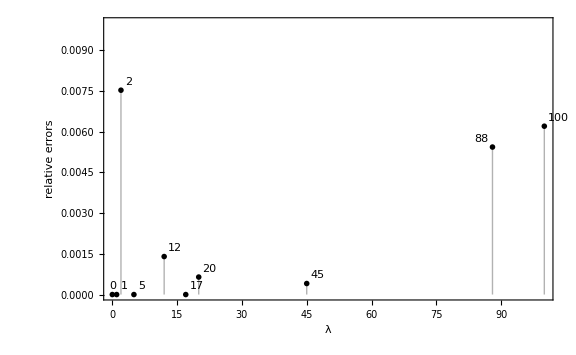

```mathematica
ListPlot[Labeled[#,#]&/@data2,Frame->True,Filling->Axis,FrameLabel->{"λ","relative errors"},PlotTheme-> "Monochrome",PlotRange->{0.0, .01},ImageSize->Large]
```